```mathematica
Clear[Lx,Ly,A,
sx2d,SX2D,sx2dp,SX2DP,
sy2d,SY2D,sy2dp,SY2DP,
cx2d,CX2D,cx2dp,CX2DP,
cy2d,CY2D,cy2dp,CY2DP,
cons,Cons]
```

```mathematica
Lx=44;
Ly=44;
A=Lx*Ly;
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sx2d[i_Integer,j_Integer]=0;

Do[Do[{sx2d[j+k Lx,j+1+k Lx]=-I/2,sx2d[j+1+k Lx,j+k Lx]=I/2},{j,1,Lx-1}],{k,0,Ly-1}]

SX2D=Table[sx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sx2dp[i_Integer,j_Integer]=0;

Do[{sx2dp[(k+1)Lx,1+k Lx]=-I/2,sx2dp[1+k Lx,(k+1)Lx]=I/2},{k,0,Ly-1}]

SX2DP=Table[sx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sy2d[i_Integer,j_Integer]=0;

Do[Do[{sy2d[k Lx+j,(k+1)Lx+j]=-I/2,sy2d[(k+1)Lx+j,k Lx+j]=I/2},{j,1,Lx}],{k,0,Ly-2}]

SY2D=Table[sy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sy2dp[i_Integer,j_Integer]=0;

Do[{sy2dp[(Ly-1)Lx+j,j]=-I/2,sy2dp[j,(Ly-1)Lx+j]=I/2},{j,1,Lx}]

SY2DP=Table[sy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cx2d[i_Integer,j_Integer]=0;

Do[Do[{cx2d[j+k Lx,j+1+k Lx]=1/2,cx2d[j+1+k Lx,j+k Lx]=1/2},{j,1,Lx-1}],{k,0,Ly-1}]

CX2D=Table[cx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cx2dp[i_Integer,j_Integer]=0;

Do[{cx2dp[(1+k)Lx,1+k Lx]=1/2,cx2dp[1+k Lx,(1+k)Lx]=1/2},{k,0,Ly-1}]

CX2DP=Table[cx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cy2d[i_Integer,j_Integer]=0;

Do[Do[{cy2d[k Lx+j,(k+1)Lx+j]=1/2,cy2d[(k+1)Lx+j,k Lx+j]=1/2},{j,1,Lx}],{k,0,Ly-2}]

CY2D=Table[cy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cy2dp[i_Integer,j_Integer]=0;

Do[{cy2dp[(Ly-1)Lx+j,j]=1/2,cy2dp[j,(Ly-1)Lx+j]=1/2},{j,1,Lx}]

CY2DP=Table[cy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------- Lattice model for a constant matrix ---------------*)
```

```mathematica
cons[i_Integer, j_Integer]:=0

Do[{cons[i,i]=1},{i,1,A}]

Cons=Table[cons[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3,HamiltonianQAHI]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
HamiltonianQAHI[t_,t0_,m_,α_]:=t*(KroneckerProduct[SX2D+α*SX2DP,σ1]+KroneckerProduct[SY2D+α*SY2DP, σ2])+KroneckerProduct[-m*Cons+t0*(CX2D+CY2D+α*CX2DP+α*CY2DP),σ3]
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------------quasicrystal--------------------------*)
```

```mathematica
Clear[Sitelocation,FlatSite,Sites, LineUp,LineDn]
```

```mathematica
Sitelocation=Table[{i,j},{i,1,Lx},{j,1,Ly}];
```

```mathematica
FlatSite=Flatten[Sitelocation];
```

```mathematica
NOrbitals=Dimensions[FlatSite][[1]]
```

3872

```mathematica
Sites=Table[{FlatSite[[i]],FlatSite[[i+1]]},{i,1,NOrbitals,2}];
```

```mathematica
(**--Equations for the two red lines--**)
```

```mathematica
LineUp[x_]:=((1+√5)/2)^-1*(x-1)+8
LineDn[x_]:=((1+√5)/2)^-1*(x-2)+6
```

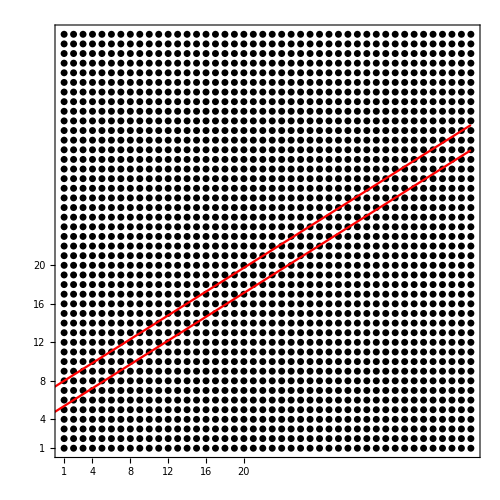

```mathematica
Show[ListPlot[Sites,PlotStyle-> {Black,PointSize[0.01]},Frame-> True,Axes-> False,PlotRange-> {{0.9,Lx+0.1},{0.9,Ly+0.1}}],
Plot[LineUp[x],{x,0,Lx},PlotStyle-> Red],
Plot[LineDn[x],{x,0,Lx},PlotStyle-> Red],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
FrameTicks-> {{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None},{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None}},
ImageSize-> 500,AspectRatio-> 1
]
```

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[Fibonup,Fibondown,TotalFibon,XList, YList, XListKron, YListKron,LogEigenValuesBott,Bott, BottIndexQuasi]
```

```mathematica
(**-----We want to count points inside the area of interest, store them in FibonupNew, and sort them into Fibonup-----**)
```

```mathematica
Clear[FibonupNew]
FibonupNew={};
```

```mathematica
(**---Points on the lines are not taken---**)
```

```mathematica
(**---That is why we calculate Floor[]+1 instead of Ceiling, and Ceiling[]-1 instead of Floor---**)
```

```mathematica
Do[Do[FibonupNew=Append[FibonupNew,x+(y-1)*Lx],{y,Max[1,Floor[LineDn[x]]+1],Min[Ly,Ceiling[LineUp[x]]-1]}],{x,1,Lx}]
```

```mathematica
FibonupNew;
```

```mathematica
Fibonlist=Sort[FibonupNew];
```

```mathematica
YList = Ceiling[Fibonlist/Lx];
```

```mathematica
XList = Fibonlist - (YList - 1)Lx;
```

```mathematica
(**Check that the list is correct**)
```

```mathematica
XList + (YList-1)*Lx - Fibonlist;
```

```mathematica
XListKron = Flatten[KroneckerProduct[XList,{1,1}],2];
```

```mathematica
YListKron = Flatten[KroneckerProduct[YList,{1,1}],2];
```

```mathematica
(**----Group the orbitals in the sites in Fibonlist ---**)
```

```mathematica
Fibonup = 2 * Fibonlist -1;
```

```mathematica
Fibondown = 2 * Fibonlist;
```

```mathematica
TotalFibon=Flatten[{Fibonup,Fibondown}];
```

```mathematica
TotalFibon = Sort[TotalFibon];
```

```mathematica
NOrbitalsQuasi=Dimensions[TotalFibon][[1]]
```

228

```mathematica
NOrbitalsQuasi/2
```

114

```mathematica
NOrbitalsOutside = NOrbitals-NOrbitalsQuasi
```

3644

```mathematica
Percentage = N[NOrbitalsQuasi/(2*A)]
```

0.0588843

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[F1,a]
```

```mathematica
F1=Table[i,{i,1,2*A}];
```

```mathematica
Dimensions[F1]
```

{3872}

```mathematica
a= Complement[F1, TotalFibon];
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[HTrial,Hfbfb,HFBFB,H2d2d,H2D2D,H2dfb,H2DFB,Hfb2d,HFB2D]
```

```mathematica
HTrial=HamiltonianQAHI[1.,1.,-1,0.0];
```

```mathematica
(*---------------------------------------------------------*)
```

```mathematica
Hfbfb[i_Integer,j_Integer]=0;
Do[
Do[
Hfbfb[i,j]=HTrial[[TotalFibon[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsQuasi}
]
HFBFB=Table[Hfbfb[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsQuasi}];
```

```mathematica
(*---------------------------------------------------------*)
```

```mathematica
H2d2d[i_Integer,j_Integer]=0;
Do[
Do[
H2d2d[i,j]=HTrial[[a[[i]],a[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsOutside}
]
H2D2D=Table[H2d2d[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsOutside}];
```

```mathematica
(*------------------------------------------------------*)
```

```mathematica
H2dfb[i_Integer,j_Integer]=0;

Do[
Do[
H2dfb[i,j]=HTrial[[a[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsQuasi}
]
H2DFB=Table[H2dfb[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsQuasi}];
```

```mathematica
(*-------------------------------------------------*)
```

```mathematica
Hfb2d[i_Integer,j_Integer]=0;

Do[
Do[
Hfb2d[i,j]=HTrial[[TotalFibon[[i]],a[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsOutside}
]
HFB2D=Table[Hfb2d[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsOutside}];
```

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[HFibonRenor,ValueFibon,VecFibon,ValVecFibon,ValFibon,OnlyEigenvalue]
```

```mathematica
HFibonRenor=HFBFB-(HFB2D.Inverse[H2D2D].H2DFB);
```

```mathematica
{ValueFibon,VecFibon}=Eigensystem[HFibonRenor];
```

```mathematica
ValVecFibon=SortBy[Transpose[{ValueFibon,VecFibon}],First];
```

```mathematica
ValFibon=Table[{j,ValVecFibon[[j,1]]},{j,1,NOrbitalsQuasi}]//Chop;
```

```mathematica
(**-----------------------------------------------------------------------------**)
```

H_PTP is gapped

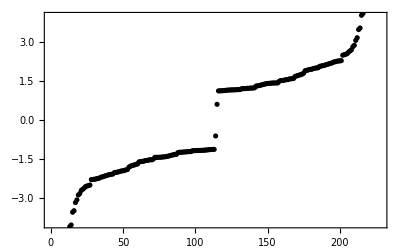

```mathematica
Show[ListPlot[ValFibon,Frame-> True,Axes-> False,BaseStyle-> 16,PlotStyle-> Black,FrameStyle-> Black,PlotRange->{All,{-4,4}}]]
```

```mathematica
Clear[HFibonRenor,ValueFibon,VecFibon,ValVecFibon,ValFibon,OnlyEigenvalue]
```

```mathematica
(**-----------------------------------------------------------------------------**)
```

H22 is gapless

```mathematica
eigenvaluesH22 = Sort[Eigenvalues[H2D2D]];
```

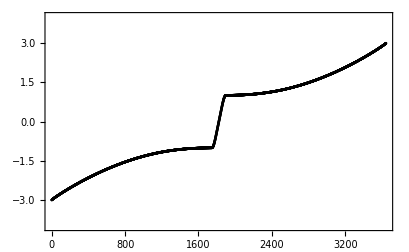

```mathematica
Show[ListPlot[Table[{i,eigenvaluesH22[[i]]},{i,1,Dimensions[eigenvaluesH22][[1]]}],Frame-> True,Axes-> False,BaseStyle-> 16,PlotStyle-> Black,FrameStyle-> Black,PlotRange->{All,{-4,4}}]]
```

```mathematica
(**-----------------------------------------------------------------------------**)
```

The parent system is gapless

```mathematica
eigenvaluesHTrial = Sort[Eigenvalues[HTrial]];
```

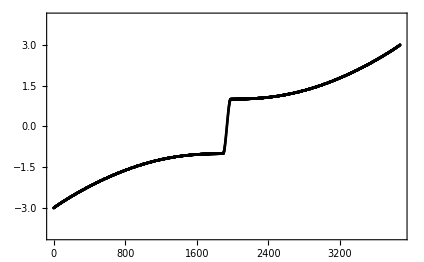

```mathematica
Show[ListPlot[Table[{i,eigenvaluesHTrial[[i]]},{i,1,Dimensions[eigenvaluesHTrial][[1]]}],Frame-> True,Axes-> False,BaseStyle-> 16,PlotStyle-> Black,FrameStyle-> Black,PlotRange->{All,{-4,4}}]]
```

```mathematica
Clear[aaa]
```

```mathematica
aaa = Sort[Re[Eigenvalues[(HFB2D.Inverse[H2D2D].H2DFB)]]]
```

{-57.2993,-56.3878,-18.8932,-18.5862,-11.0936,-10.9059,-7.67409,-7.53671,-5.72292,-5.61338,-4.44748,-4.35592,-3.54353,-3.46494,-2.86915,-2.80069,-2.34875,-2.2887,-1.93788,-1.8851,-1.60824,-1.56189,-1.34057,-1.30002,-1.12116,-1.08586,-0.939844,-0.909316,-0.788925,-0.762681,-0.662434,-0.639977,-0.555709,-0.536533,-0.465124,-0.448731,-0.387916,-0.373848,-0.32206,-0.309917,-0.266114,-0.255573,-0.219023,-0.20984,-0.179875,-0.171869,-0.147707,-0.140731,-0.121441,-0.115358,-0.0999567,-0.0946296,-0.0822246,-0.0775175,-0.0673894,-0.0631805,-0.0547996,-0.0509882,-0.0439828,-0.0404888,-0.034593,-0.031349,-0.0263528,-0.0232936,-0.0190102,-0.0160656,-0.0123226,-0.00941475,-0.00605831,-0.00310141,-3.48257×10^-16,-2.74201×10^-16,-1.80575×10^-16,-1.64348×10^-16,-7.85507×10^-17,-7.46685×10^-17,-5.54384×10^-17,-4.96859×10^-17,-1.21604×10^-17,-1.02984×10^-17,-4.93013×10^-18,-1.32792×10^-18,-3.09721×10^-19,-9.8383×10^-32,-3.33525×10^-34,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.84182×10^-49,7.54776×10^-35,4.35804×10^-33,1.6393×10^-32,2.75444×10^-32,2.48828×10^-31,1.72595×10^-19,2.18128×10^-18,7.37696×10^-18,1.09296×10^-17,1.37325×10^-17,1.38143×10^-17,1.59812×10^-17,1.92233×10^-17,5.98963×10^-17,6.28842×10^-17,6.8585×10^-17,8.48297×10^-17,1.1933×10^-16,3.52642×10^-16,4.69606×10^-16,0.00310141,0.00605831,0.00941475,0.0123226,0.0160656,0.0190102,0.0232936,0.0263528,0.031349,0.034593,0.0404888,0.0439828,0.0509882,0.0547996,0.0631805,0.0673894,0.0775175,0.0822246,0.0946296,0.0999567,0.115358,0.121441,0.140731,0.147707,0.171869,0.179875,0.20984,0.219023,0.255573,0.266114,0.309917,0.32206,0.373848,0.387916,0.448731,0.465124,0.536533,0.555709,0.639977,0.662434,0.762681,0.788925,0.909316,0.939844,1.08586,1.12116,1.30002,1.34057,1.56189,1.60824,1.8851,1.93788,2.2887,2.34875,2.80069,2.86915,3.46494,3.54353,4.35592,4.44748,5.61338,5.72292,7.53671,7.67409,10.9059,11.0936,18.5862,18.8932,56.3878,57.2993}

```mathematica
2*Max[aaa]
```

114.599

```mathematica
lvsDeltaEPBC={{20,109.323525211403},{24,131.19292695662952},{28,151.68021255173983},{32,173.60464948987908},{36,194.05783181658052},{40,215.9918189618297},{44,234.2859912941605},{48,258.371994594021}}
```

{{20,109.324},{24,131.193},{28,151.68},{32,173.605},{36,194.058},{40,215.992},{44,234.286},{48,258.372}}

```mathematica
lvsDeltaEOBC={{20,50.85349216171575},{24,62.69998750037272},{28,72.12827067923402},{32,84.29582349285805},{36,93.36260570183538},{40,105.53012310873606},{44,114.59866679672383}}
```

{{20,50.8535},{24,62.7},{28,72.1283},{32,84.2958},{36,93.3626},{40,105.53},{44,114.599}}

```mathematica
PBCInverseTable=Table[{1/(lvsDeltaEPBC[[i]][[1]]),1/(lvsDeltaEPBC[[i]][[2]])},{i,1,Dimensions[lvsDeltaEPBC][[1]]}]
```

{{1/20,0.00914716},{1/24,0.00762236},{1/28,0.00659282},{1/32,0.00576021},{1/36,0.0051531},{1/40,0.0046298},{1/44,0.00426829},{1/48,0.00387039}}

```mathematica
OBCInverseTable=Table[{1/(lvsDeltaEOBC[[i]][[1]]),1/(lvsDeltaEOBC[[i]][[2]])},{i,1,Dimensions[lvsDeltaEOBC][[1]]}]
```

{{1/20,0.0196643},{1/24,0.015949},{1/28,0.0138642},{1/32,0.011863},{1/36,0.0107109},{1/40,0.00947597},{1/44,0.00872611}}

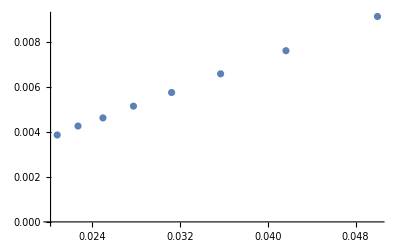

```mathematica
ListPlot[PBCInverseTable]
```

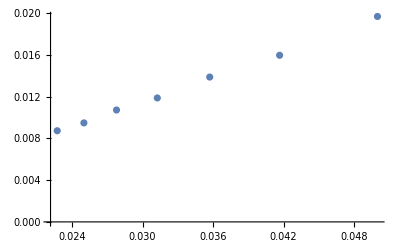

```mathematica
ListPlot[OBCInverseTable]
```

```mathematica
Fit[PBCInverseTable,{1,x},x]
```

0.00014621+0.179921 x

```mathematica
Fit[OBCInverseTable,{1,x},x]
```

-0.000462225+0.399294 x